```mathematica
G[k_,s_,Ω_,temper_]:=Block[{a=1/(-1+ⅇ^((23200 Ω)/(2temper))),b=ⅇ^((23200 Ω)/(2temper))/(-1+ⅇ^((23200 Ω)/(2temper)))},ⅇ^(-s(a+b))/Ω(a/b)^(k/2)*BesselI[Abs[k],2 √a √b s]];
```

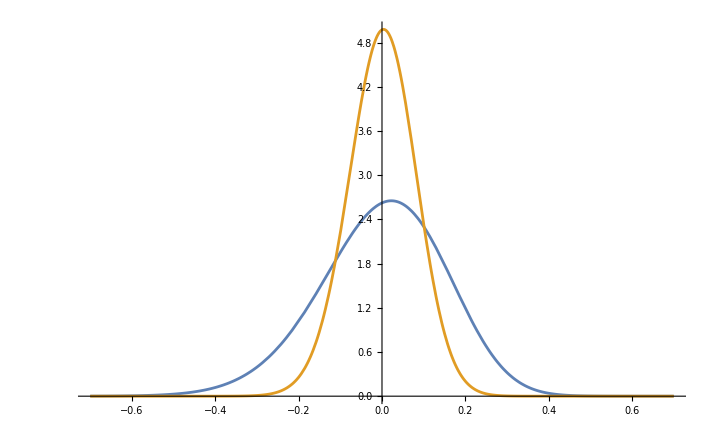

```mathematica
Plot[{G[(ϵ-6*0.055)/0.055,6,0.055,300],G[(ϵ-6*0.02)/0.02,6,0.02,300]},{ϵ,-0.7,0.7},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"single_line.txt",Table[{x,G[(x-6*0.055)/0.055,6,0.055,300]},{x,-1.0,0.7,0.01}],"Table"]
```